0.00736842

1.00882

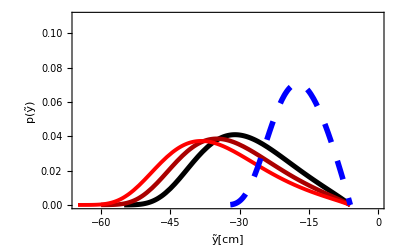

```mathematica
(*This Mathematica code models the water table depth (WTD) dynamics for Rhizophora mangle (Red mangrove) under various salinity conditions.It accounts for the impact of salinity on evapotranspiration,soil moisture retention,and hydraulic conductivity.The model uses ecohydrological parameters and functions to simulate the water table depth distribution and related hydrological processes.*)

(*Parameters Taylor Rizophora (Red mangrove) *)
α=0.78; (* rainfall annual average depth [cm]*)
Subscript[λ, 0]=0.337;(*rainfall annual frequency [1/day]*)
Subscript[ET, max]=0.42; (* potential evapotranspiration [cm/day]*)
Subscript[b, c]=0.022;(* β coefficient of ET/ETmax=f(C(i)), it takes into account the salt-tollerance of the plant*)
CT=8.76;(* salinity stress threshold [g/l]*)
m=0.164; (* pore size index *)
Subscript[k, s]=1.84; (*  saturated hydraulic conductivit*)
n=0.4; (* porosity Best *)
Subscript[ψ, s]=-6 ;(* saturared matric potential*)
y0=-10;(*exterrnal water body depth [cm]*)
ymin=-61;(* minimum observed water depth*)

ψfc[C_]:=Subscript[ψ, s]*sfcc[C]^(-1/m) (*Function defining matric potential as a function of salinity*)

Subscript[k, l] =ETMAX/(y0-ymin-Subscript[ψ, s])(*constant of proportionality for loamy sand soil*)
zr=30; (*Root zone depth[cm],depth where most of the root mass is located*)
V=1;(*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n;
C2=-0.0627;(* Integration constant*)

ETmaxC[C_]:=Subscript[ET, max]*(1+V*Subscript[b, c] CT-V*Subscript[b, c] C) (*Function defining ETmax as a function of salinity (C)*)
sfc=((0.05*Subscript[ET, max])/Subscript[k, s])^(m/(2+3m));(*soil moistute field capacity [-]*)
sfcc[C_]:=((0.05*ETmaxC[C])/Subscript[k, s])^(m/(2+3m))(*soil moistute field capacity with salinity effect[-]*)
v=Subscript[ET, max]/(1+c0*zr);
vc[C_]=ETmaxC[C]/(1+c0*zr);
yc=Subscript[ψ, s]*sfc^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/Subscript[k, s] sfc^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/Subscript[k, s]];(*critical value of water depth*)
ycc[C_]:=Subscript[ψ, s]*sfcc[C]^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[C])/Subscript[k, s] sfcc[C]^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[C])/Subscript[k, s]](*critical value of water depth with salinity effect*)

λ[y_]=Subscript[λ, 0]; (* frequency of precipitation*)
β[y_]=n-n(1+((sfc)^(-1/(2m))-1)*(y/yc))^(-2m); (* yield, ratio between the water volume released from the storage and the corresponding variation in water level*)
βc[y_,C_]=n-n(1+((sfcc[C])^(-1/(2m))-1)*(y/ycc[C]))^(-2m);(* yield with salinity effect*)
fl[y_]:=Subscript[k, l](y0-y-Subscript[ψ, s]) (* lateral flow*)
f[y_]=(Subscript[k, l](y0-y-Subscript[ψ, s])-Subscript[ET, max])/β[y];(* see Tamea et al 2009*)
fc[y_,C_]=(Subscript[k, l](y0-y-Subscript[ψ, s])-ETmaxC[C])/βc[y,C];
g[y_]=1/β[y];(* see Tamea et al 2009*)
gc[y_,C_]=1/βc[y,C];


Subscript[p, Y][y_]:=1/(Subscript[ET, max]+Subscript[k, l] (y-y0+Subscript[ψ, s]))C1 ⅇ^(1/2 n (-(2 (y+(sfc^(1/(2 m)) yc)/((-1+2 m) (-1+sfc^(1/(2 m))))-((1+((-1+sfc^(-1/(2 m))) y)/yc)^(-2 m) (y-sfc^(1/(2 m)) y+sfc^(1/(2 m)) yc))/((-1+2 m) (-1+sfc^(1/(2 m))))))/α-(Subscript[λ, 0] (2 m Log[Subscript[ET, max]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,((-1+sfc^(1/(2 m))) Subscript[ET, max]-Subscript[k, l] ((-1+sfc^(1/(2 m))) y0-sfc^(1/(2 m)) yc-(-1+sfc^(1/(2 m))) Subscript[ψ, s]))/((-1+sfc^(1/(2 m))) (Subscript[ET, max]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfc^(1/(2 m)) yc Subscript[k, l])/((-1+sfc^(1/(2 m))) (Subscript[ET, max]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(m Subscript[k, l])-(Subscript[λ, 0] (-2 Log[Subscript[ET, max]+Subscript[k, l] (y-y0+Subscript[ψ, s])]-((1+((-1+sfc^(-1/(2 m))) y)/yc)^(-2 m) Hypergeometric2F1[2 m,2 m,1+2 m,((-1+sfc^(1/(2 m))) Subscript[ET, max]-Subscript[k, l] ((-1+sfc^(1/(2 m))) y0-sfc^(1/(2 m)) yc-(-1+sfc^(1/(2 m))) Subscript[ψ, s]))/((-1+sfc^(1/(2 m))) (Subscript[ET, max]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] ((((-1+sfc^(1/(2 m))) y-sfc^(1/(2 m)) yc) Subscript[k, l])/((-1+sfc^(1/(2 m))) (Subscript[ET, max]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/m))/Subscript[k, l])) (n-n (1+((-1+sfc^(-1/(2 m))) y)/yc)^(-2 m))(*pdf(y) without salinity effect*)



Subscript[Subscript[p, Y], c][y_,C]:=-1/(ETmaxC[C]+Subscript[k, l] (y-y0+Subscript[ψ, s]))C2 ⅇ^(-(n (y+(sfcc[C]^(1/(2 m)) ycc[C])/((-1+2 m) (-1+sfcc[C]^(1/(2 m))))-(sfcc[C]^(1/(2 m)) (1+((-1+sfcc[C]^(-1/(2 m))) y)/ycc[C])^(1-2 m) ycc[C])/((-1+2 m) (-1+sfcc[C]^(1/(2 m))))-(α Log[ETmaxC[C]+Subscript[k, l] (y-y0+Subscript[ψ, s])] Subscript[λ, 0])/Subscript[k, l]-((1+((-1+sfcc[C]^(-1/(2 m))) y)/ycc[C])^(-2 m) α Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[C](-1+sfcc[C]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[C]^(1/(2 m)) y0+sfcc[C]^(1/(2 m)) ycc[C]+(-1+sfcc[C]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[C]^(1/(2 m))) (ETmaxC[C]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] Subscript[λ, 0] ((((-1+sfcc[C]^(1/(2 m))) y-sfcc[C]^(1/(2 m)) ycc[C]) Subscript[k, l])/((-1+sfcc[C]^(1/(2 m))) (ETmaxC[C]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/(2 m Subscript[k, l])+(α Subscript[λ, 0] (2 m Log[ETmaxC[C]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[C] (-1+sfcc[C]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[C]^(1/(2 m)) y0+sfcc[C]^(1/(2 m)) ycc[C]+(-1+sfcc[C]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[C]^(1/(2 m))) (ETmaxC[C]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfcc[C]^(1/(2 m)) ycc[C] Subscript[k, l])/((-1+sfcc[C]^(1/(2 m))) (ETmaxC[C]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(2 m Subscript[k, l])))/α) (n-n (1+((-1+sfcc[C]^(-1/(2 m))) y)/ycc[C])^(-2 m))(*pdf(y) with salinity effect*)

Subscript[p, Subscript[Y, N]][x_]=Re[Subscript[p, Y][y]/.y->(x-Subscript[ψ, s]) ];(*pdf of water table depth calculated as derived distribution of the pdf of saturation depth*)
pYNC[z_,C_]=Re[Subscript[Subscript[p, Y], c][y,C]/.y->(z-Subscript[ψ, s])];
I1=NIntegrate[pYNC[z,16],{z,-55,Subscript[ψ, s]}];
I2=NIntegrate[pYNC[z,12],{z,-60,Subscript[ψ, s]}];
I3=NIntegrate[pYNC[z,CT],{z,-65,Subscript[ψ, s]}];
I4=NIntegrate[pYNC[z,35],{z,-32,Subscript[ψ, s]}];
pdfRedManfrove1=Plot[pYNC[z,16]/I1,{z,-55,Subscript[ψ, s]},PlotStyle->{Black,Thickness[0.009]},PlotRange->{{-65,0},{0,0.11}},AxesOrigin->{Subscript[ψ, s],0},BaseStyle->{FontFamily->"Arial",FontSize->18},AxesLabel->{StyleForm["ỹ[cm]",FontSize->18],StyleForm["p(ỹ)",FontSize->18]}];
pdfRedManfrove2=Plot[pYNC[z,12]/I2,{z,-60,Subscript[ψ, s]},PlotStyle->{Darker[Red],Thickness[0.008]},PlotRange->All,AxesOrigin->{Subscript[ψ, s],0},BaseStyle->{FontFamily->"Arial",FontSize->18},AxesLabel->{StyleForm["ỹ[cm]",FontSize->18],StyleForm["p(ỹ)",FontSize->18]}];
pdfRedManfrove3=Plot[pYNC[z,CT]/I3,{z,-65,Subscript[ψ, s]},PlotStyle->{Red,Thickness[0.007]},PlotRange->All,AxesOrigin->{Subscript[ψ, s],0},BaseStyle->{FontFamily->"Arial",FontSize->18},AxesLabel->{StyleForm["ỹ[cm]",FontSize->18],StyleForm["p(ỹ)",FontSize->18]}];
pdfRedManfrove4=Plot[pYNC[z,35]/I4,{z,-32,Subscript[ψ, s]},PlotStyle->{Dashing[Large],Blue,Thickness[0.01]},PlotRange->All,AxesOrigin->{Subscript[ψ, s],0},BaseStyle->{FontFamily->"Arial",FontSize->18},AxesLabel->{StyleForm["ỹ[cm]",FontSize->18],StyleForm["p(ỹ)",FontSize->18]}];
ETRedManfrove=Plot[ETmaxC[C]/ETMAX,{C,CT,35},PlotStyle->{Black,Thickness[0.012]},PlotRange->All,AxesOrigin->{0,0},BaseStyle->{FontFamily->"Arial",FontSize->18},AxesLabel->{StyleForm["C",FontSize->18],StyleForm["ET(C)",FontSize->18]}];
SetOptions[Plot,Frame->True,GridLines->None,PlotStyle->{Black,Thickness[0.012]},PlotRange->All,AxesOrigin->{0,0}];
P1=Show[pdfRedManfrove1,pdfRedManfrove2,pdfRedManfrove3,pdfRedManfrove4]
```